# Mapping of indoor environments with the Wolfram language and Raspberry Pi

## Isaac Ayala

Instituto Tecnológico y de Estudios Superiores de Monterrey

## The Simulatenous Localization and Mapping problem

How can a robot navigate in an unknown environment while constantly building and updating a map of its surroundings?

```mathematica
Import["https://docs.google.com/drawings/d/1Q0GFAjnZ0Xq88e9UwkY0FH6XKjf3g2ABR7ZCFEvqzmw/pub?w=960&h=720"]
```

-Graphics-

```mathematica
Import["https://4.bp.blogspot.com/-Pa4x4XBFvN8/U-UIozfl3kI/AAAAAAAAAmc/cd34AVKW6Gs/s1600/chicken-or-egg.jpg"]
```

-Graphics-

## Solution

## Make a robot!

#### Algorithm

```mathematica
Import["https://docs.google.com/drawings/d/1KbLprC-P1dsqzqODmBAHIIJ_D5AMz2gINF2Ngm53XuY/pub?w=915&h=765"]
```

-Graphics-

#### Graphical User Interface

#### Data visualization

## Live Demo!

### Map

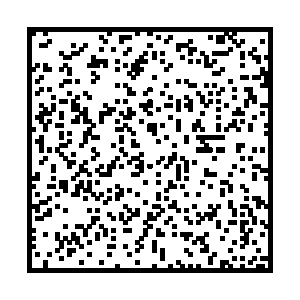

```mathematica
a4=Table[{-30,i},{i,-30,30}];
b4=Table[{30,i},{i,-30,30}];
c4=Table[{i,-30},{i,-30,30}];
d4=Table[{i,30},{i,-30,30}];
borders4=Join@@{a4,b4,c4,d4};
obstacles4=Table[{RandomInteger[{-30,30}],RandomInteger[{-30,30}]},{i,800}];
map4=DeleteCases[Join[borders4,obstacles4],{0,0}];
Graphics[Rectangle/@map4,ImageSize->300,PlotRange->{{-30,31},{-30,31}}]
```

#### Code

#### Functions

```mathematica
updateSensorsSim[currentPosition_List, map_List]:=Block[{collisions,sensorState},

collisions={
MemberQ[map,{currentPosition[[1]],currentPosition[[2]]+1}],
MemberQ[map,{currentPosition[[1]]+1,currentPosition[[2]]}],
MemberQ[map,{currentPosition[[1]],currentPosition[[2]]-1}],
MemberQ[map,{currentPosition[[1]]-1,currentPosition[[2]]}]};

sensorState=Table[If[collisions[[i]]==True,1,0],{i,Length[collisions]}];
sensorState
]

getTimeDifference[tNow_,tBefore_]:=Module[{},Round[QuantityMagnitude[UnitConvert[tNow-tBefore,"Seconds"]]]]

updatePosition[currentTime_,statusOld_List,speed_List]:=Module[{newPosition,Δt=getTimeDifference[currentTime,statusOld[[1]]]},
newPosition=Piecewise[{{Round[statusOld[[2]]+{0,Δt}*speed], statusOld[[3]]=="Forward"}, {Round[statusOld[[2]]-{0,Δt}*speed], statusOld[[3]]=="Back"}, {Round[statusOld[[2]]-{Δt,0}*speed], statusOld[[3]]=="Left"}, {Round[statusOld[[2]]+{Δt,0}*speed], statusOld[[3]]=="Right"}, {statusOld[[2]], statusOld[[3]]=="Stop"}}]
]

updateWalls2[location_,statusOld_List,sensorsNow_List]:=Module[{x=location[[1]],y=location[[2]],newWalls,blockPerimeter},

blockPerimeter=sensorsNow*{{x,y+1},{x+1,y},{x,y-1},{x-1,y}};

blockPerimeter=DeleteCases[blockPerimeter,{0,0}];

newWalls=Join[statusOld[[5]],blockPerimeter];

If[Length[newWalls]>1,newWalls=DeleteCases[newWalls,{}],Nothing];

newWalls]

updateMap[location_List,currentTime_,statusOld_List]:=Module[{newMap=statusOld[[6]],mapSurface,Δt=getTimeDifference[currentTime,statusOld[[1]]]},
mapSurface=Piecewise[{{Table[{location[[1]],statusOld[[2,2]]+i},{i,Δt}], statusOld[[3]]=="Forward"}, {Table[{location[[1]],statusOld[[2,2]]-i},{i,Δt}], statusOld[[3]]=="Back"}, {Table[{statusOld[[2,1]]+i,location[[2]]},{i,Δt}], statusOld[[3]]=="Right"}, {Table[{statusOld[[2,1]]-i,location[[2]]},{i,Δt}], statusOld[[3]]=="Left"}, {{statusOld[[2]]}, statusOld[[3]]=="Stop"}}];
If[statusOld[[3]]!="Stop",newMap=Join[newMap,mapSurface]];
newMap]

updateDirection2[dirs_List,buttons_List,current_String]:=
Module[{i,obstacles,placeholder,placeholder2,nextdir,placeholder3},
obstacles=Table[1-buttons[[i]],{i,Length[buttons]}];
placeholder3=DeleteCases[dirs,"Stop"];
placeholder2=DeleteCases[placeholder3*obstacles,0];
If[MemberQ[placeholder3*obstacles,current],nextdir=current,nextdir=RandomChoice[placeholder2]]]
```

#### Robot simulation

```mathematica
position={0,0};
velocity={2,2}; 

discoveredMap={{0,0}};
walls={{}};
directions={"Forward","Right","Back","Left"};
sensors=updateSensorsSim[position,map4];
pause=1;

nextDirection=RandomChoice[directions];

status={TimeObject[Now],position,nextDirection,sensors,walls,discoveredMap};
test={};
```

```mathematica
position={0,0};
velocity={2,2}; 

discoveredMap={{0,0}};
walls={{}};
directions={"Forward","Right","Back","Left"};
sensors=updateSensorsSim[position,map4];
pause=1;

nextDirection=RandomChoice[directions];

status={TimeObject[Now],position,nextDirection,sensors,walls,discoveredMap};
test={};

Do[
timestampNew=TimeObject[Now];
previousStatus=status;
positionNew=updatePosition[timestampNew,previousStatus,velocity];
sensors=updateSensorsSim[positionNew,map4];

wallsNew=updateWalls2[positionNew,previousStatus,sensors];

mapNew=updateMap[positionNew,timestampNew,previousStatus];

nextDirection=updateDirection2[directions,sensors,previousStatus[[3]]];
status={timestampNew,positionNew,nextDirection,sensors,wallsNew,mapNew};
test=Append[test,status];
Pause[pause];
,{loop,20}]
```

### Results

```mathematica
Manipulate[Overlay[{
Graphics[{Green,Rectangle/@test[[frame,6]],Blue,Rectangle[test[[frame,2]]],Style[Rectangle/@DeleteCases[test[[frame,5]],{}],Red]},
PlotRange->{{test[[frame,2,1]]-20,test[[frame,2,1]]+20},{test[[frame,2,2]]-20,test[[frame,2,2]]+20}},ImageSize->{400}],

Framed[Graphics3D[{Blue,Cuboid[Join[test[[frame,2]],{0}]],Green,Cuboid/@Table[Join[test[[frame,6,i]],{-1}],{i,Length[test[[frame,6]]]}],
Style[Cuboid/@Table[If[test[[frame,5,i]]=={},Nothing,Join[DeleteCases[test[[frame,5,i]],{}],{0}]],{i,Length[test[[frame,5]]]}],Red]},

Boxed->False,PlotRange->{{test[[frame,2,1]]-5,test[[frame,2,1]]+5},{test[[frame,2,2]]-5,test[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]]
},Alignment->{Right,Top}],{frame,1,Length[test],1}]
```

## Conclusions

You can control robots with Mathematica!

It is possible to create a SLAM solution with digital logic

It’s best to add PID control to the hardware